# Meshing The Drums

Some folks had some problems with the drum meshes.  I think there were different bits of problems for the FENICS and GRIDAP folks.  As I understand it the “boundary tags” were not working for the some of the GridApp folks and the FENICS folks currently need to “fake” the boundary with an equation.

The two may need different solutions but lets think about what would be the easiest way to do things.

## The circle is easy!

Defined entirely by the radius R

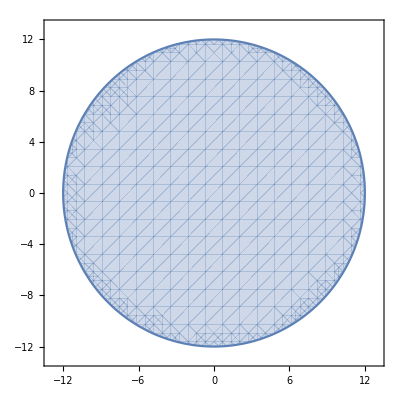

```mathematica
R=12;
RegionPlot[ x^2+y^2≤R^2,{x, -13,13},{y,-13,13}]
```

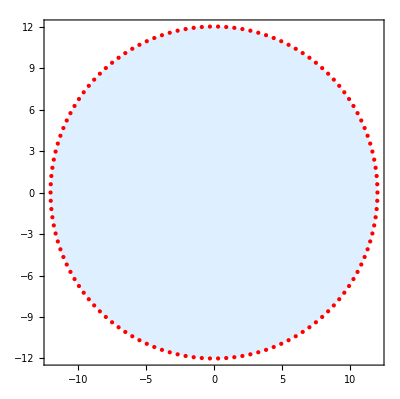

```mathematica
R=12.0; n=126;
BorderPoints=Table[R{Cos[θ],Sin[θ]},{θ,2π/n, 2π, 2π/n}];
Graphics[{{LightBlue,Polygon[BorderPoints]},{Red, Point[BorderPoints]}},Frame->True]
```

## The Square and Rectangle Can be done together!

Defined by the two side lengths 2a and 2b along with the rounded of radius r.  The center of each rounding off circle is displaced {r,r} towards the inside of the rectangle from the corner.

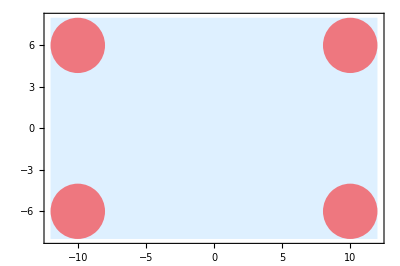

```mathematica
{a,b,r}={12.0,8.0,2.0};
Graphics[{
{LightBlue,Rectangle[{-a,-b},{a,b}]},
{Opacity[0.5], Red,
Disk[{a-r,b-r},r],
Disk[{-a+r,b-r},r],
Disk[{-a+r,-b+r},r],
Disk[{a-r,-b+r},r]}},Frame->True]
```

We can make the rounded off rectangle we want by putting edges together.  All I really need are dots around the outside of each quarter circle in the correct ccw order!  Lets think about it for a second.

{a,b}  we need 0≤θ≤π/2.

{-a,b}  we need π/2≤θ≤π.

{-a,-b}  we need π≤θ≤3π/2.

{a,-b}  we need 3π/2≤θ≤2π.

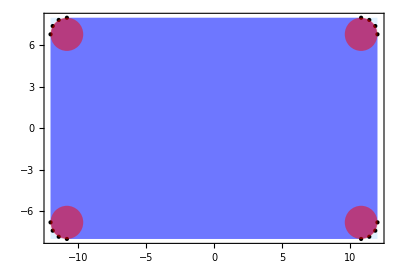

```mathematica
n=6;
BorderPoints=Join[
Table[{a-r,b-r}+r {Cos[θ],Sin[θ]},{θ,0,π/2,π/n}],
Table[{-a+r,b-r}+r {Cos[θ],Sin[θ]},{θ,π/2,π,π/n}],
Table[{-a+r,-b+r}+r {Cos[θ],Sin[θ]},{θ,π,3π/2,π/n}],
Table[{a-r,-b+r}+r {Cos[θ],Sin[θ]},{θ,3π/2,2π,π/n}]];
Graphics[{
{LightBlue,Rectangle[{-a,-b},{a,b}]},
{Opacity[0.5],Blue,Polygon[BorderPoints]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,
Disk[{a-r,b-r},r],
Disk[{-a+r,b-r},r],
Disk[{-a+r,-b+r},r],
Disk[{a-r,-b+r},r]}},Frame->True]
```

## Triangles!

We can probably do triangles the same way by rounding of the edges using some trig.  I need three points (counter clock wise) to define a triangle and a rounding radius r.  I can easily compute the center of the triangle.

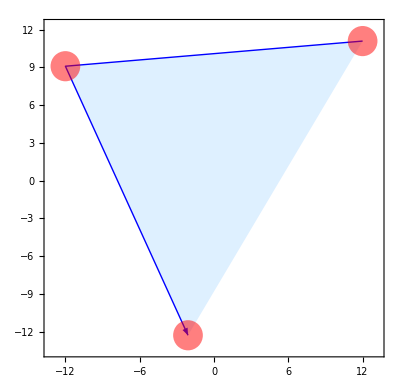

```mathematica
{p1,p2,p3}={{12.0,11.1},{-12.0,9.1},{-2.1,-12.3}};
r=1.2;
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3}]},
{Opacity[0.5], Red,Disk[p1,r],Disk[p2,r],Disk[p3,r]}
},Frame->True]
```

I need to move each circle in along the line bisecting each angle until it is just inside the triangle.  At that point the circle is tangent to both edges!  I am going to add guide lines in the middle of each angle!  The easiest way to compute the bisectors is to compute the “incenter” of the triangle

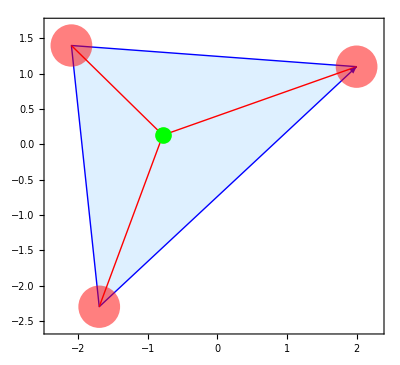

```mathematica
{p1,p2,p3}={{2.0,1.1},{-2.1,1.4},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,pCenter}],Arrow[{p2,pCenter}],Arrow[{p3,pCenter}] },
{PointSize[0.03],Green,Point[pCenter]},
{Opacity[0.5], Red,Disk[p1,r],Disk[p2,r],Disk[p3,r]}
},Frame->True]
```

Now we are going to do some simple trig (on the board) to work out how far to move each disk in!  We will check we did it correctly by computing the correct values of the shifts on the pic below.

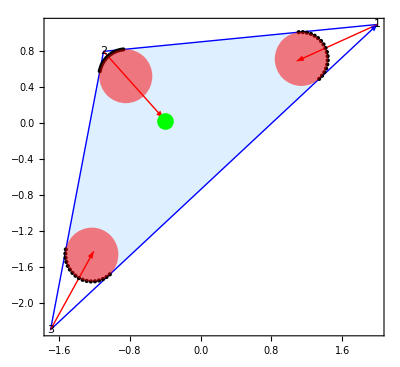

```mathematica
{p1,p2,p3}={{2.0,1.1},{-1.1,0.8},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
(* make unit vectors towards in center *)
{τ1,τ2,τ3}= Map[Normalize,{pCenter-p1,pCenter-p2,pCenter-p3}];
(* make unit vectors pependicular to the τs *)
{n1,n2,n3}=Map[{-#⟦2⟧,#⟦1⟧}&,{τ1,τ2,τ3}];
{θ1,θ2,θ3}= {
0.5 ArcCos[((p2-p1).(p3-p1))/(Norm[p2-p1] Norm[p3-p1])],
0.5 ArcCos[((p3-p2).(p1-p2))/(Norm[p3-p2] Norm[p1-p2])],
0.5 ArcCos[((p2-p3).(p1-p3))/(Norm[p2-p3] Norm[p1-p3])]};

{d1,d2,d3}={r/Sin[θ1],r/Sin[θ2],r/Sin[θ3]};
(* Compute Complementary Angles *)
{θc1,θc2,θc3}={π/2-θ1,π/2-θ2,π/2-θ3};
(* Build Border Points *)
m=8;
BorderPoints=Join[
Table[ p1+τ1 d1 - r (τ1 Cos[θ]+n1 Sin[θ]),{θ,-θc1,θc1,θc1/m}],
Table[ p2+τ2 d2 - r (τ2 Cos[θ]+n2 Sin[θ]),{θ,-θc2,θc2,θc2/m}],
Table[ p3+τ3 d3 - r (τ3 Cos[θ]+n3 Sin[θ]),{θ,-θc3,θc3,θc3/m}]
];
(* Check that it works *)
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,p1+τ1}],Arrow[{p2,p2+τ2}],Arrow[{p3,p3+τ3}] },
{PointSize[0.03],Green,Point[pCenter]},
{Black,Text["1",p1],Text["2",p2],Text["3",p3]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,Disk[p1+d1 τ1,r],Disk[p2+d2 τ2,r],Disk[p3+d3 τ3,r]}
},Frame->True];
Graphics[{
{LightBlue,Polygon[BorderPoints]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,p1+τ1}],Arrow[{p2,p2+τ2}],Arrow[{p3,p3+τ3}] },
{PointSize[0.03],Green,Point[pCenter]},
{Black,Text["1",p1],Text["2",p2],Text["3",p3]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,Disk[p1+d1 τ1,r],Disk[p2+d2 τ2,r],Disk[p3+d3 τ3,r]}
},Frame->True]
```

## Semi Circle!

The semi circle is actually a slice off the top of a circle with the corners rounded off. 

It is defined by a big radius “R” a distance “d” up from the diameter and a rounding radius “r”.  It is easier (unless you love trig) to work out how far the disks need to move in now.

If we make up a recipe (or a thing to solve) we can work out what is “just-right”.

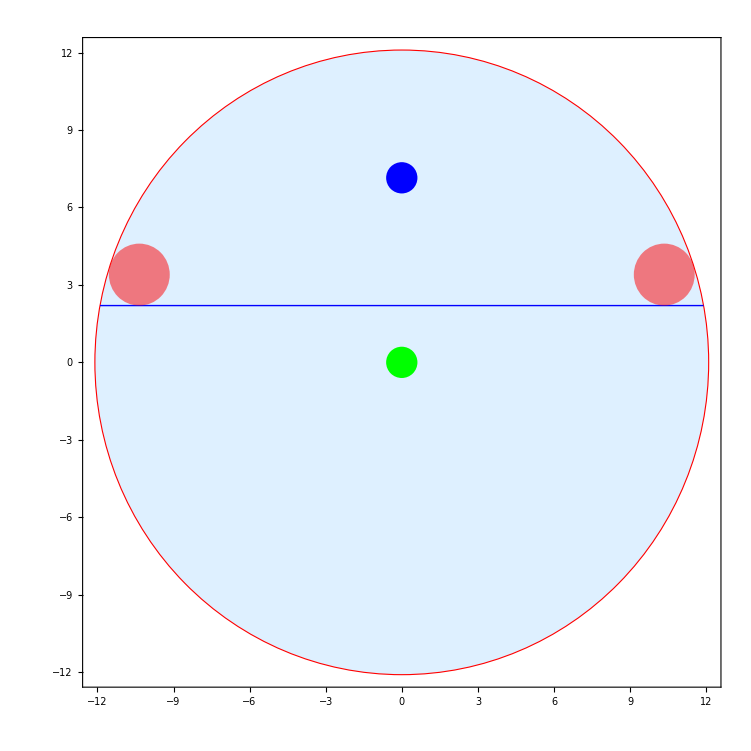

```mathematica
{R,d,r}={12.1,2.2,1.2};
x1=√(R^2-d^2);
s1=1.55;
Graphics[{
{LightBlue,EdgeForm[Red],Disk[{0,0},R]},
{Blue, Line[{{-x1,d},{x1,d}}]},
{PointSize[0.03],Green,Point[{0,0}]},
{PointSize[0.03],Blue,Point[{0,(R+d)/2}]},
{Opacity[0.5], Red,Disk[{-x1+s1,d+r},r],Disk[{x1-s1,d+r},r]}
},Frame->True]
```

I need to find the value of s when the big circle
	x^2+y^2=R^2
and the little circle radius r centered at {x1-s,d+r} 
	(x-(x1-s))^2+(y-(d+r))^2=r^2
are tangent. Expand the complicated circle to get
	x^2-2x(x1-s)+(x1-s)^2+y^2-2 y(d+r)+(d+r)^2=r^2
and substitute x^2+y^2->R^2 to get
	R^2-2x(x1-s)+(x1-s)^2-2 y(d+r)+(d+r)^2=r^2
then move the things you know (R^2, (d+r)^2) to the RHS to get
	-2x(x1-s)+(x1-s)^2-2 y(d+r)=r^2-R^2-(d+r)^2
and solve for y as a function of everything else
	y=-1/(2(d+r))(r^2-R^2-(d+r)^2+2x(x1-s)-(x1-s)^2)

```mathematica
{p1,p2,p3}={{2.0,1.1},{-2.1,1.4},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,pCenter}],Arrow[{p2,pCenter}],Arrow[{p3,pCenter}] },
{PointSize[0.03],Green,Point[pCenter]},
{Opacity[0.5], Red,Disk[p1,r],Disk[p2,r],Disk[p3,r]}
},Frame->True]
```

-Graphics-

Now we are going to do some simple trig (on the board) to work out how far to move each disk in!  We will check we did it correctly by computing the correct values of the shifts on the pic below.

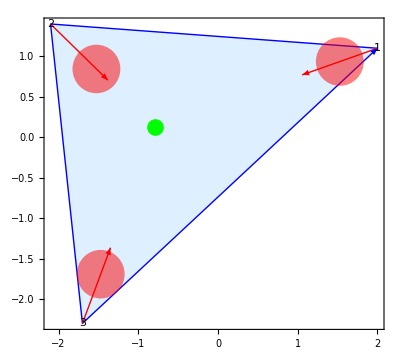

```mathematica
{p1,p2,p3}={{2.0,1.1},{-2.1,1.4},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
{τ1,τ2,τ3}= Map[Normalize,{pCenter-p1,pCenter-p2,pCenter-p3}];
{d1,d2,d3}={0.5,0.8,0.65};
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,p1+τ1}],Arrow[{p2,p2+τ2}],Arrow[{p3,p3+τ3}] },
{PointSize[0.03],Green,Point[pCenter]},
{Black,Text["1",p1],Text["2",p2],Text["3",p3]},
{Opacity[0.5], Red,Disk[p1+d1 τ1,r],Disk[p2+d2 τ2,r],Disk[p3+d3 τ3,r]}
},Frame->True]
```